Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->1];
datafullwithheading=Import["../data/ccm1_data_modified.csv"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
Print["Dataset Length: ",Dimensions@datafull[[All,9]]]
```

Dataset Length: {459203}

```mathematica
Magnify[TableView[datafullwithheading],0.6];
```

```mathematica
Print["Width Feature Data Summary: ",Counts@(Head/@datafull[[All,9]])]
Print["Width Zero Values: ",Count[datafull[[All,9]],0]]
Print["Thickness Feature Data Summary: ",Counts@(Head/@datafull[[All,10]])]
Print["Thickness Zero Values: ",Count[datafull[[All,10]],0]]
```

Width Feature Data Summary: <|Real→397873,Integer→61183,String→147|>

Width Zero Values: 61183

Thickness Feature Data Summary: <|Real→397860,Integer→61199,String→144|>

Thickness Zero Values: 61199

Modifications in the Dataset

```mathematica
densitycolumn=datafull[[All,11]]/(datafull[[All,9]]*datafull[[All,10]]*datafull[[All,12]]);
```

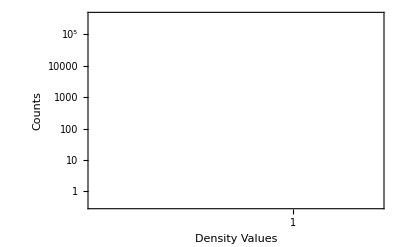

```mathematica
Histogram[Select[DeleteCases[densitycolumn,ComplexInfinity],#>0&],{10^-4},ScalingFunctions->{"Log","Log"},PlotRange->{{0.8,1.1},All},Frame->True,FrameLabel->{"Density Values","Counts"}]
```

Width Feature

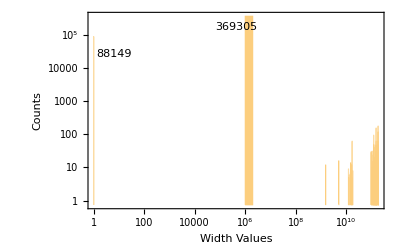

```mathematica
Histogram[datafull[[All,9]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,ChartLabels->Placed[{88149,369305},{{0.07,0.8},Top},Framed[#,FrameMargins->1,Background->LightYellow]&],FrameLabel->{"Width Values","Counts"}]
```

```mathematica
widthmodified=Table[If[StringQ@i,i,If[(RealDigits@i)[[2]]>4,i/10^((RealDigits@i)[[2]]-4),i,i]],{i,datafull[[All,9]]}]
Counts@(Head/@widthmodified)
```

{1240.,1240.,1240.,1240.,1240.,1240.,1240.,1230.,1230.,1230.,1230.,1230.,1230.,1230.,1220.,1220.,1220.,1220.,1220.,459165,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1350.,1350.,1350.,1350.,NA,NA}
 |  |  |  |

<|Real→397873,Integer→61183,String→147|>

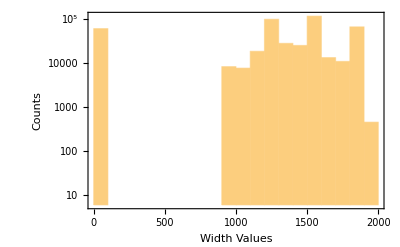

```mathematica
Histogram[widthmodified,ScalingFunctions->"Log",PlotRange->{{0,2000},All},Frame->True,FrameLabel->{"Width Values","Counts"}]
```

Thickness Feature

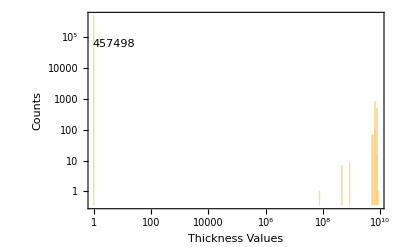

```mathematica
Histogram[datafull[[All,10]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,ChartLabels->Placed[457498,{0.07,0.85},Framed[#,FrameMargins->1,Background->LightYellow]&],FrameLabel->{"Thickness Values","Counts"}]
```

```mathematica
thicknessmodified=Table[If[StringQ@i,i,If[(RealDigits@i)[[2]]>2,i/10^((RealDigits@i)[[2]]-2),i,i]],{i,datafull[[All,10]]}]
Counts@(Head/@thicknessmodified)
```

{87.,87.,87.,87.,87.,87.,87.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,459148,0,0,0,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,NA,NA}
 |  |  |  |

<|Real→397860,Integer→61199,String→144|>

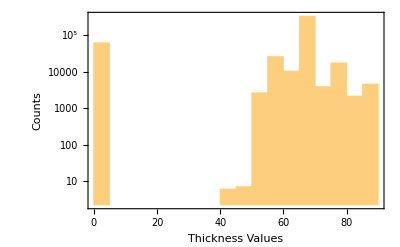

```mathematica
Histogram[thicknessmodified,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"}]
```

Time Windows Generation by Data Partitioning

```mathematica
datafull[[All,9]]=widthmodified;
datafull[[All,10]]=thicknessmodified;
data=Table[Take[datafull,UpTo@i],{i,{46497,91690,138440,183584,230005,275844,320350,367179,413106,459203}}];
```

```mathematica
(* Export["data_with_time_windows2.mx",data] *)
```

Investigation of Constraints Impact in Time Windows

Simple Association Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindows=snetworkdatasingleintimewindows[9,10];]
```

{2162.75,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraphsinglenodes[widthdataintimewindows[[1]][[i]],widthdataintimewindows[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

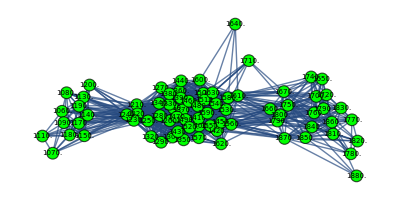
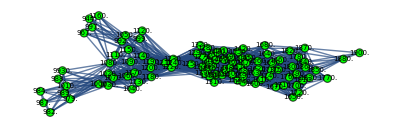
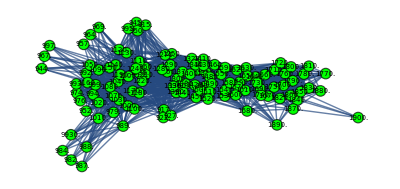
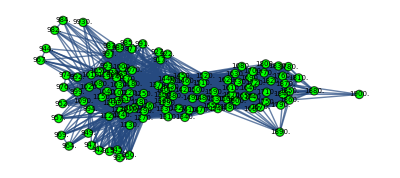
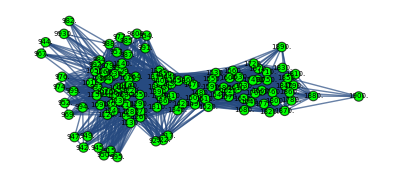
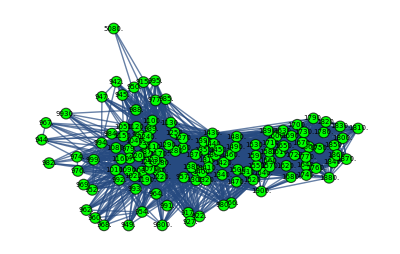
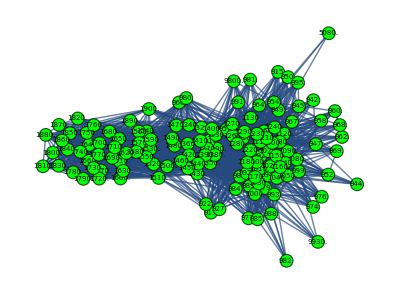
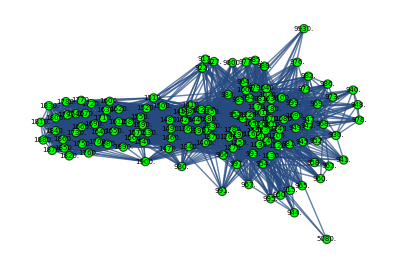
{{-Graphics-,78},{-Graphics-,101},{-Graphics-,118},{-Graphics-,124},{-Graphics-,126},{-Graphics-,132},{-Graphics-,134},{-Graphics-,142},{-Graphics-,143},{-Graphics-,145}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.806576,-0.982937},{0.770325,-0.885228},{0.909307,-0.9352},{0.940662,-0.96362},{0.936794,-0.954259},{0.950441,-0.977428},{0.943662,-0.981075},{0.92873,-0.976994},{0.913954,-0.964238},{0.880782,-0.938651}}

{{0.531068,-0.789318},{0.532997,-0.664498},{0.694625,-0.702197},{0.720999,-0.674561},{0.765535,-0.74416},{0.816172,-0.783676},{0.805377,-0.790045},{0.788447,-0.789135},{0.773046,-0.796311},{0.70724,-0.756691}}

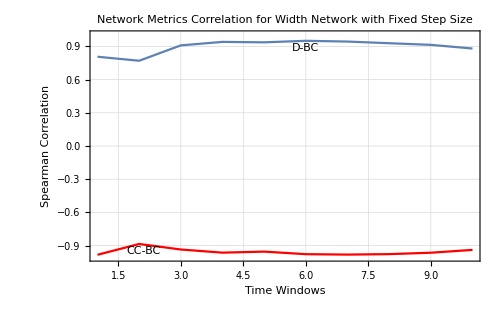
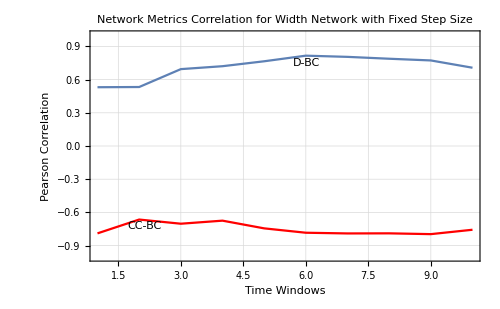

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-16.3855},{2,-28.2984},{3,-11.643},{4,-6.81793},{5,-8.6635},{6,-5.98649},{7,-7.90497},{8,-12.8777},{9,-17.8417},{10,-26.1208}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-6.1844},{2,-6.28408},{3,-7.44833},{4,-7.55609},{5,-7.7609},{6,-8.34804},{7,-8.31869},{8,-8.53835},{9,-8.60248},{10,-7.90532}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-54.0725},{2,-75.9149},{3,-61.0315},{4,-63.6026},{5,-54.3278},{6,-45.4448},{7,-51.7454},{8,-60.8709},{9,-71.4917},{10,-87.2258}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.50092},{2,-4.25071},{3,-5.16854},{4,-4.77387},{5,-5.6314},{6,-6.30177},{7,-6.31103},{8,-6.4964},{9,-6.74542},{10,-6.03788}}

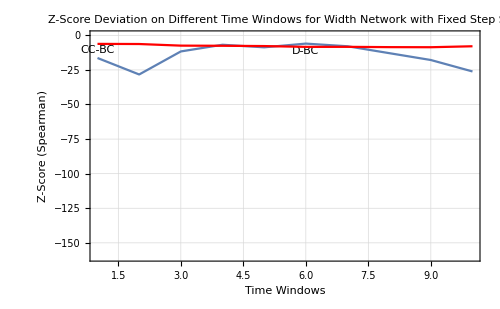
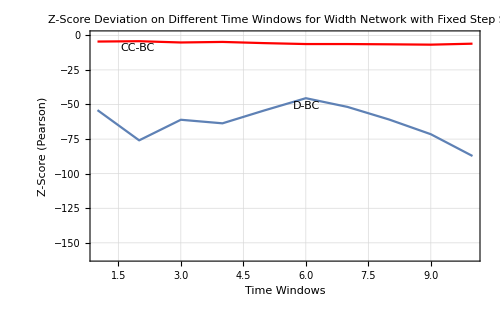

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-160,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-160,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindows=snetworkdatasingleintimewindows[10,10];]
```

{2211.65,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraphsinglenodes[thicknessdataintimewindows[[1]][[i]],thicknessdataintimewindows[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

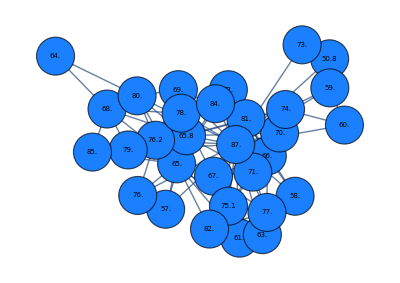
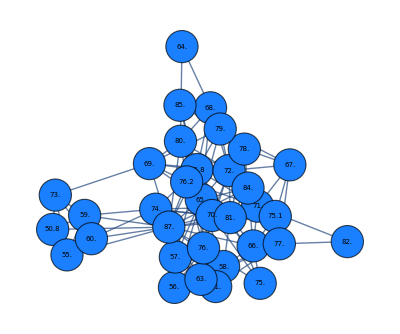
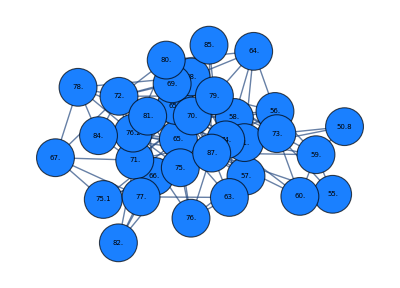
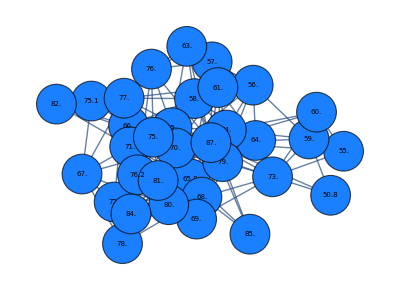
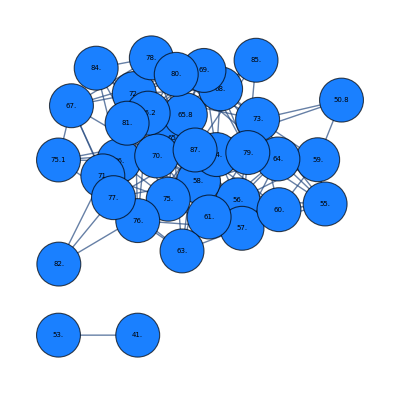
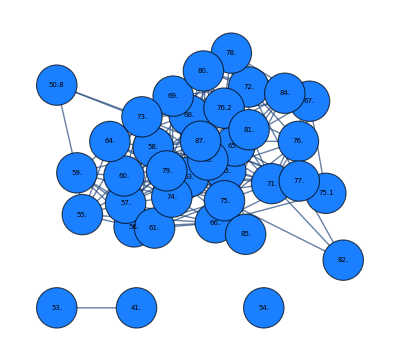
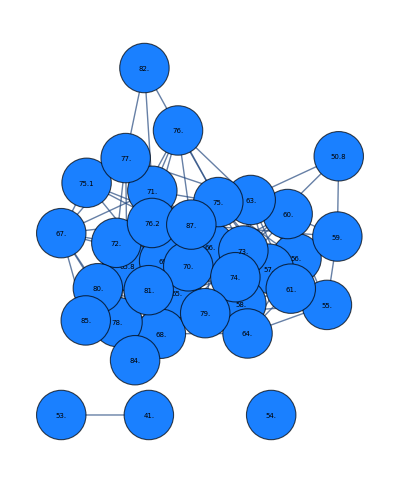
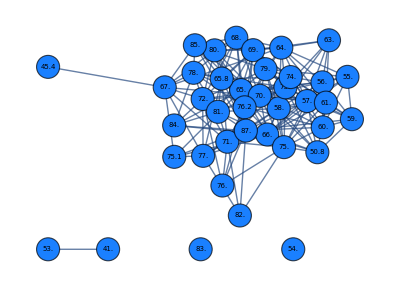
{{-Graphics-,31},{-Graphics-,34},{-Graphics-,34},{-Graphics-,34},{-Graphics-,36},{-Graphics-,37},{-Graphics-,37},{-Graphics-,39},{-Graphics-,40},{-Graphics-,40}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.908271,-0.880325},{0.863248,-0.800216},{0.901889,-0.852818},{0.94249,-0.897248},{0.934236,-0.504541},{0.906451,-0.362709},{0.920079,-0.356312},{0.917583,-0.193539},{0.900666,-0.330468},{0.926147,-0.350301}}

{{0.888923,-0.577143},{0.861959,-0.50747},{0.800672,-0.617502},{0.805816,-0.515503},{0.794726,-0.313224},{0.762246,-0.184459},{0.75713,-0.14069},{0.730214,-0.0577165},{0.668448,-0.136053},{0.656736,-0.124955}}

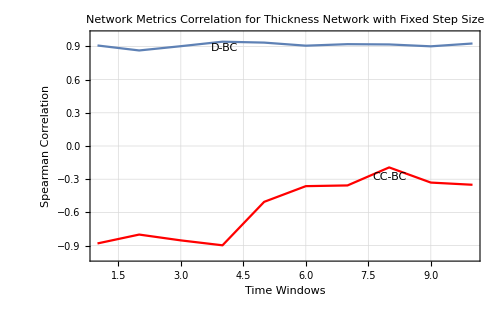
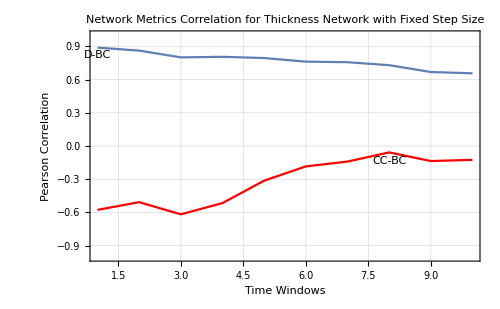

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.00268934},{2,-1.4703},{3,-0.431911},{4,0.806989},{5,0.393188},{6,-0.463191},{7,-0.0730414},{8,-0.191993},{9,-0.79344},{10,0.0485323}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.42738},{2,-3.22597},{3,-3.32448},{4,-3.64317},{5,-1.3673},{6,-0.534494},{7,-0.455313},{8,0.470379},{9,-0.400905},{10,-0.439187}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.169815},{2,-1.16157},{3,-3.46797},{4,-3.23599},{5,-3.65755},{6,-5.27257},{7,-5.50861},{8,-6.38345},{9,-8.55756},{10,-9.90258}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-2.26158},{2,-1.8464},{3,-2.22812},{4,-1.59436},{5,-0.369536},{6,0.435474},{7,0.779488},{8,1.31635},{9,0.754288},{10,0.932737}}

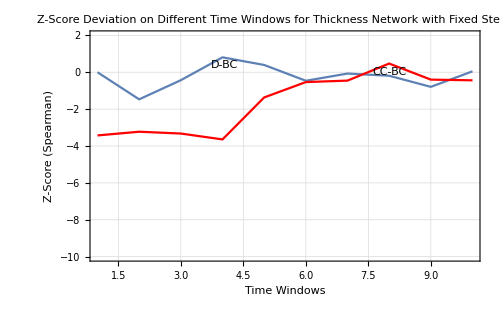
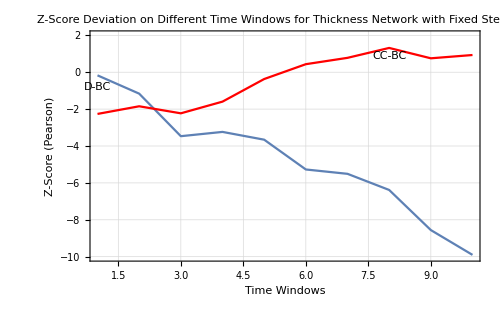

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"]}
```

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,15,10];]
```

{2001.64,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

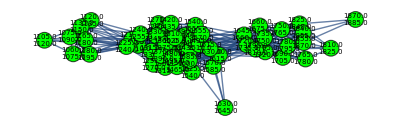
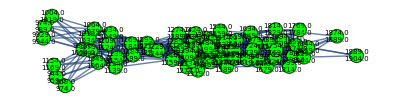
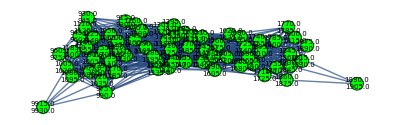
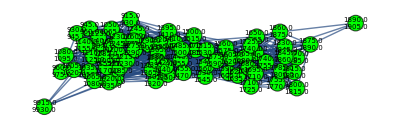
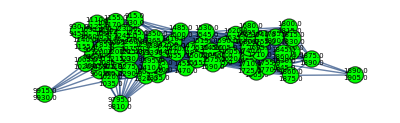
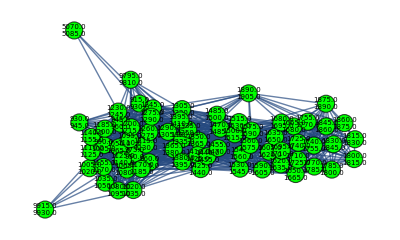
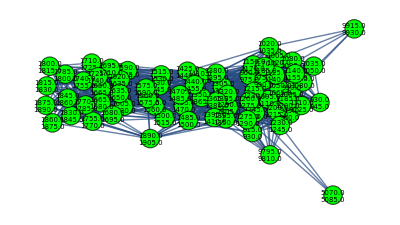
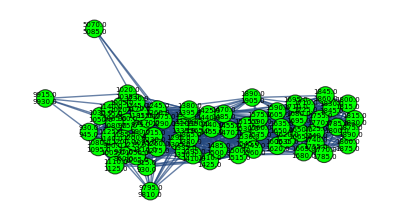
{{-Graphics-,52},{-Graphics-,64},{-Graphics-,67},{-Graphics-,67},{-Graphics-,68},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,70}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.696902,-0.970305},{0.708457,-0.930315},{0.836866,-0.933418},{0.787239,-0.937612},{0.74055,-0.93598},{0.832012,-0.973099},{0.766533,-0.973994},{0.789687,-0.981219},{0.76951,-0.986116},{0.757333,-0.924038}}

{{0.516085,-0.877985},{0.558297,-0.739024},{0.645105,-0.719585},{0.638847,-0.745658},{0.613413,-0.794671},{0.677391,-0.787154},{0.624231,-0.798807},{0.610484,-0.796431},{0.628464,-0.85741},{0.603446,-0.741984}}

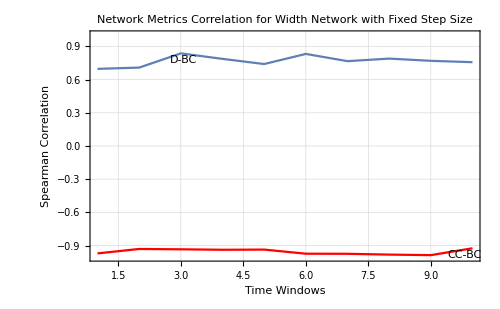
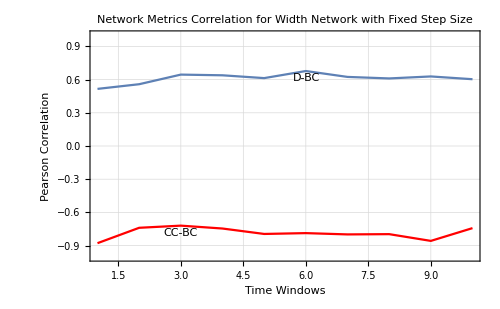

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-14.4752},{2,-20.1787},{3,-11.1504},{4,-15.9198},{5,-21.8161},{6,-12.8552},{7,-20.8482},{8,-17.42},{9,-19.5119},{10,-19.8065}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.56019},{2,-5.07561},{3,-4.9158},{4,-4.86035},{5,-4.84958},{6,-5.43619},{7,-5.08627},{8,-5.29162},{9,-5.3995},{10,-4.87927}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-31.8818},{2,-37.1705},{3,-35.846},{4,-36.4513},{5,-45.5718},{6,-37.8765},{7,-45.4412},{8,-46.7046},{9,-44.7637},{10,-47.3229}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.09634},{2,-3.68183},{3,-3.38631},{4,-3.45613},{5,-3.774},{6,-4.03435},{7,-3.76421},{8,-3.89626},{9,-4.31255},{10,-3.57121}}

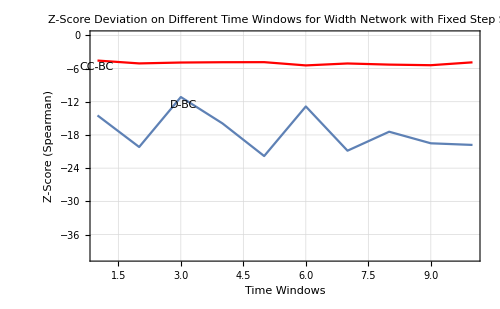
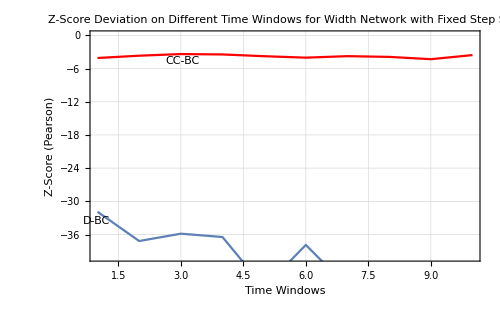

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.05,10];]
```

{4776.22,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

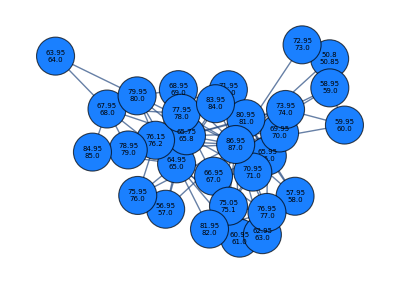
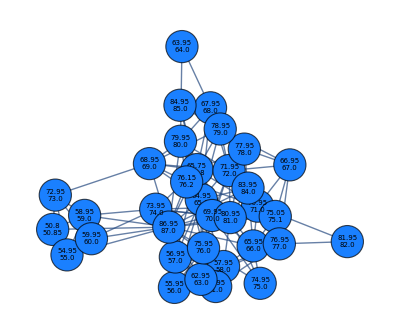
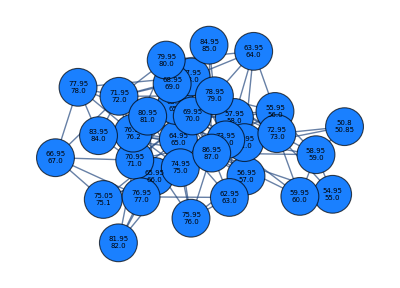
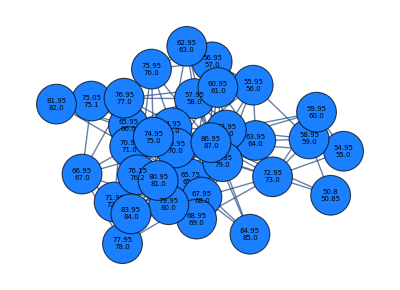
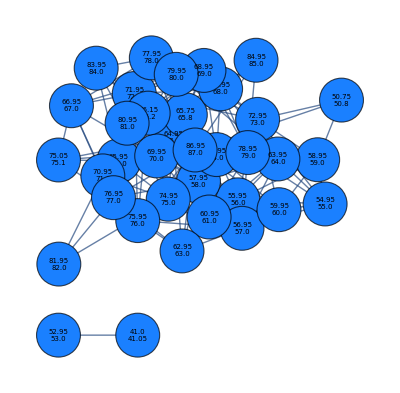
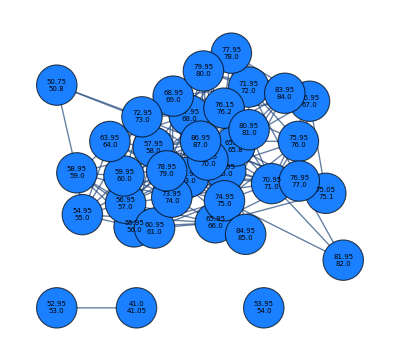
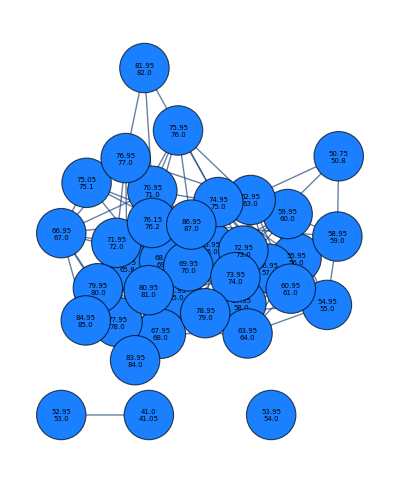
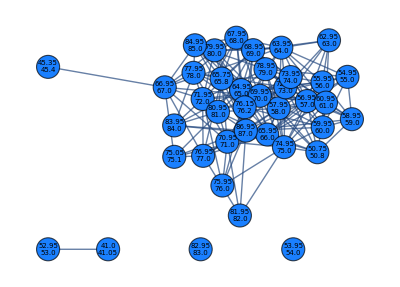
{{-Graphics-,31},{-Graphics-,34},{-Graphics-,34},{-Graphics-,34},{-Graphics-,36},{-Graphics-,37},{-Graphics-,37},{-Graphics-,39},{-Graphics-,40},{-Graphics-,40}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.908271,-0.880325},{0.863248,-0.800216},{0.901889,-0.852818},{0.94249,-0.897248},{0.934236,-0.504541},{0.906451,-0.362709},{0.920079,-0.356312},{0.917583,-0.193539},{0.900666,-0.330468},{0.926147,-0.350301}}

{{0.888923,-0.577143},{0.861959,-0.50747},{0.800672,-0.617502},{0.805816,-0.515503},{0.794726,-0.313224},{0.762246,-0.184459},{0.75713,-0.14069},{0.730214,-0.0577165},{0.668448,-0.136053},{0.656736,-0.124955}}

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"]}
```

{-Graphics-,-Graphics-}

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.00268934},{2,-1.4703},{3,-0.431911},{4,0.806989},{5,0.393188},{6,-0.463191},{7,-0.0730414},{8,-0.191993},{9,-0.79344},{10,0.0485323}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.42738},{2,-3.22597},{3,-3.32448},{4,-3.64317},{5,-1.3673},{6,-0.534494},{7,-0.455313},{8,0.470379},{9,-0.400905},{10,-0.439187}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.169815},{2,-1.16157},{3,-3.46797},{4,-3.23599},{5,-3.65755},{6,-5.27257},{7,-5.50861},{8,-6.38345},{9,-8.55756},{10,-9.90258}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-2.26158},{2,-1.8464},{3,-2.22812},{4,-1.59436},{5,-0.369536},{6,0.435474},{7,0.779488},{8,1.31635},{9,0.754288},{10,0.932737}}

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"]}
```

{-Graphics-,-Graphics-}

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdatawithfxdbucketintimewindows=snetworkdatafxdbucketintimewindows[9,55,10];]
```

{1978.38,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdatawithfxdbucketintimewindows[[1]][[i]],widthdatawithfxdbucketintimewindows[[2]][[i]],1.5,7,600,Green],{i,Range@10}];
```

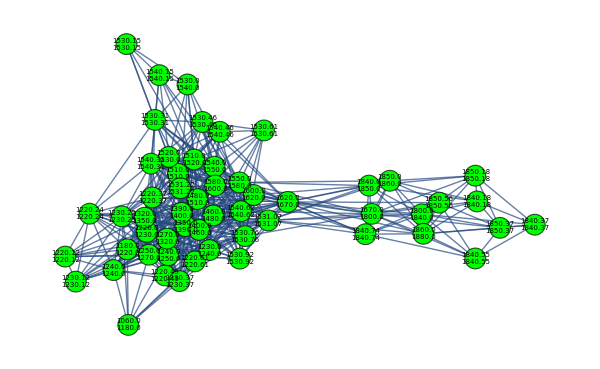
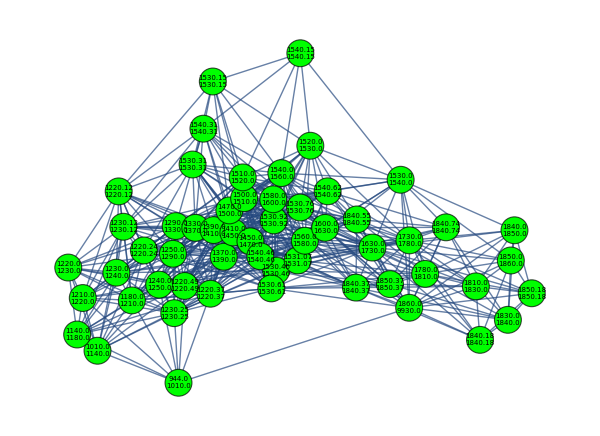
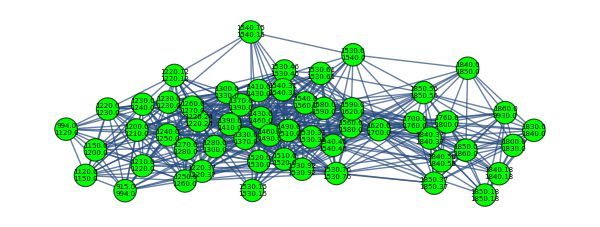
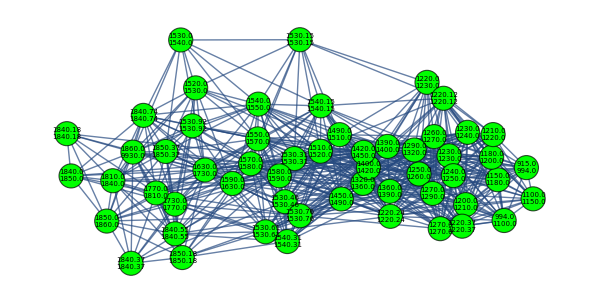
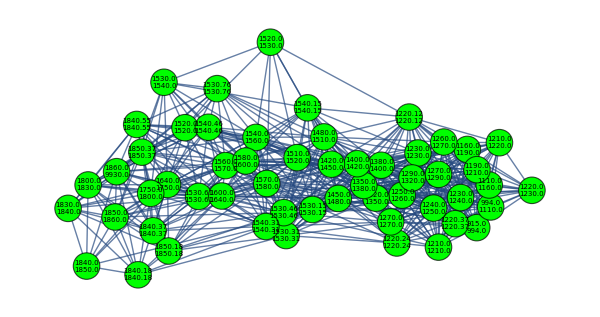
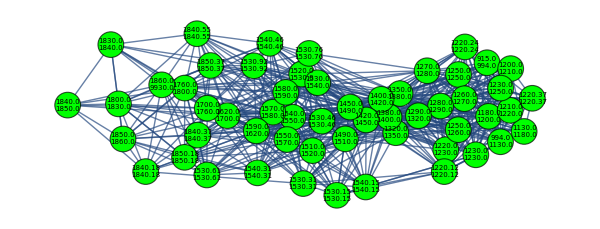
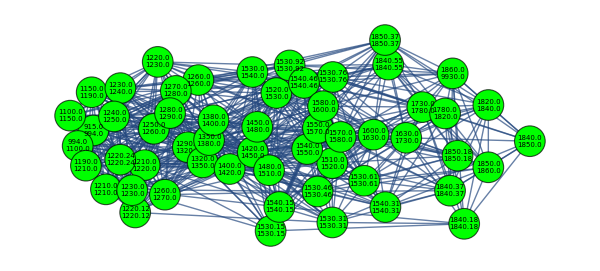
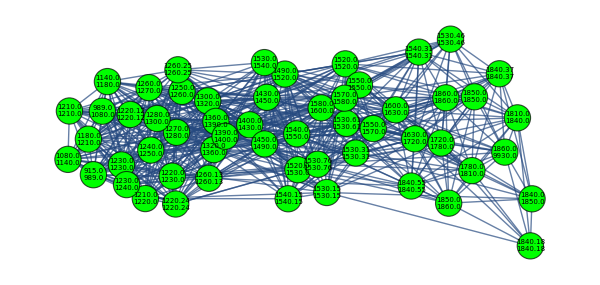
{{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.741802,-0.870626},{0.775723,-0.849066},{0.830995,-0.830399},{0.82525,-0.849932},{0.732975,-0.866518},{0.784763,-0.963507},{0.699183,-0.860638},{0.78438,-0.914152},{0.775948,-0.933685},{0.810433,-0.911364}}

{{0.48491,-0.668412},{0.665766,-0.748351},{0.720323,-0.738531},{0.678901,-0.739757},{0.730021,-0.762858},{0.818228,-0.810805},{0.769861,-0.768017},{0.742278,-0.841775},{0.814536,-0.800502},{0.77351,-0.843375}}

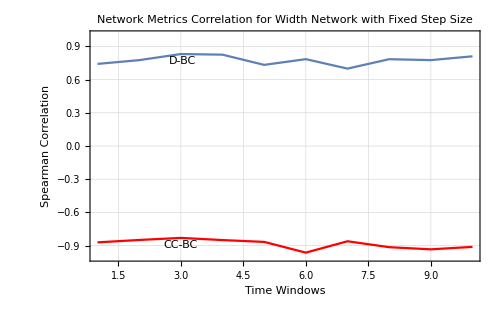
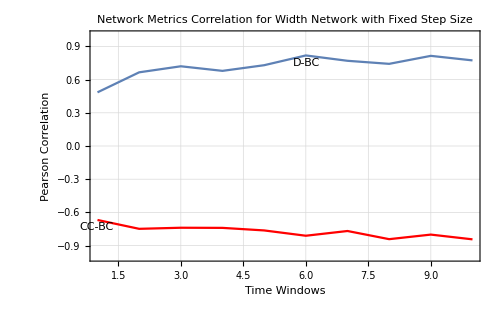

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-13.4572},{2,-12.1346},{3,-7.85406},{4,-9.00249},{5,-15.1289},{6,-11.4914},{7,-18.4508},{8,-12.8759},{9,-13.2058},{10,-11.2197}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.25655},{2,-3.87505},{3,-3.59119},{4,-3.96889},{5,-3.86315},{6,-4.45661},{7,-3.79573},{8,-4.12567},{9,-3.94343},{10,-3.88229}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-35.6687},{2,-24.3192},{3,-19.1565},{4,-24.5624},{5,-20.4774},{6,-12.0433},{7,-17.4249},{8,-20.9484},{9,-13.1069},{10,-17.6575}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-2.83598},{2,-3.21822},{3,-3.05105},{4,-3.2251},{5,-3.16283},{6,-3.53713},{7,-3.17299},{8,-3.7141},{9,-3.1288},{10,-3.46063}}

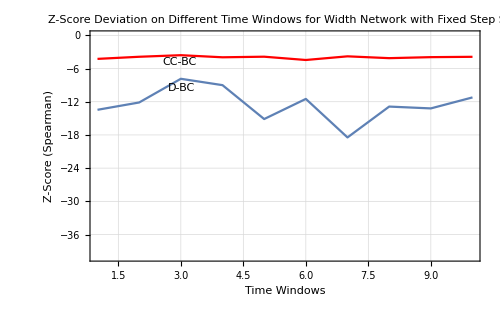
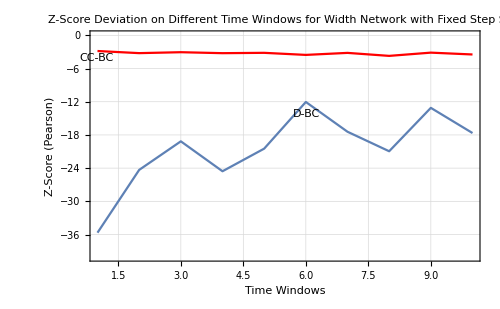

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdatawithfxdbucketintimewindows=snetworkdatafxdbucketintimewindows[10,55,10];]
```

{3701.96,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdatawithfxdbucketintimewindows[[1]][[i]],thicknessdatawithfxdbucketintimewindows[[2]][[i]],1.5,7,600,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

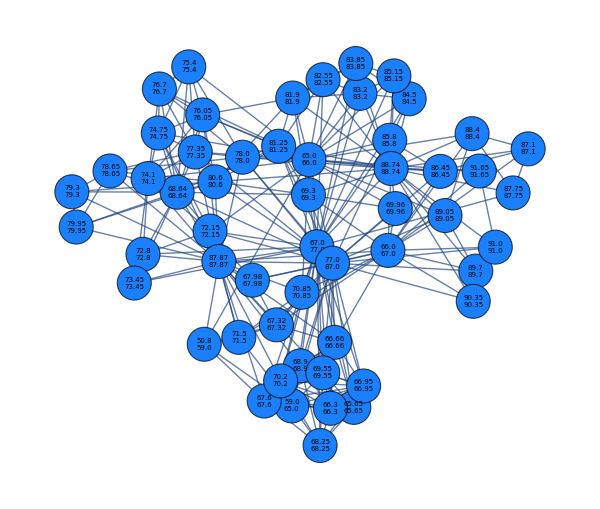
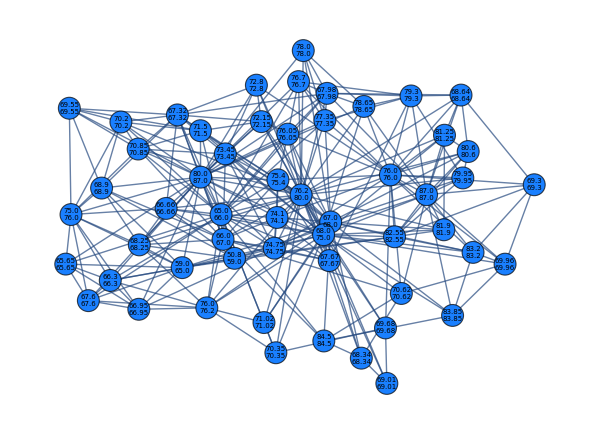
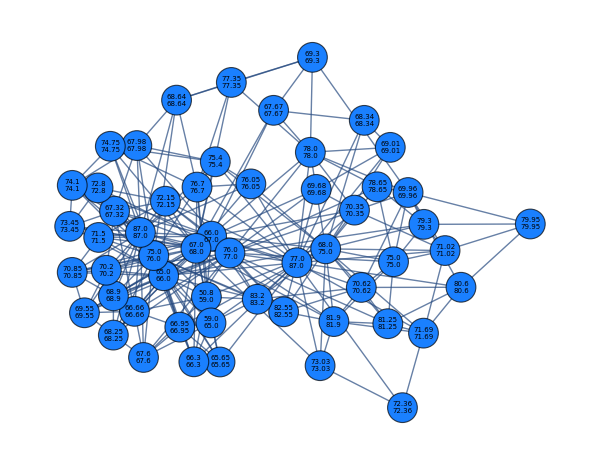
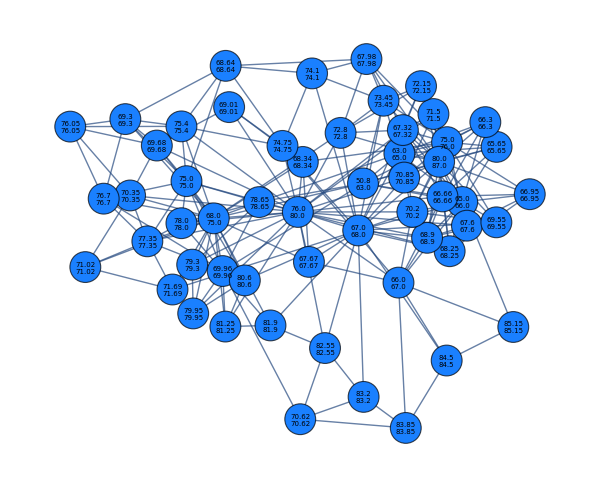
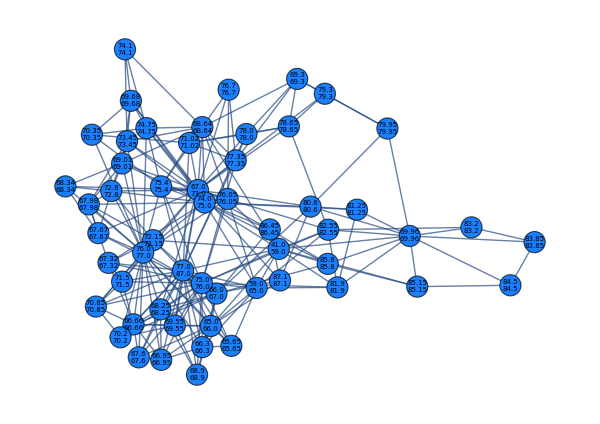
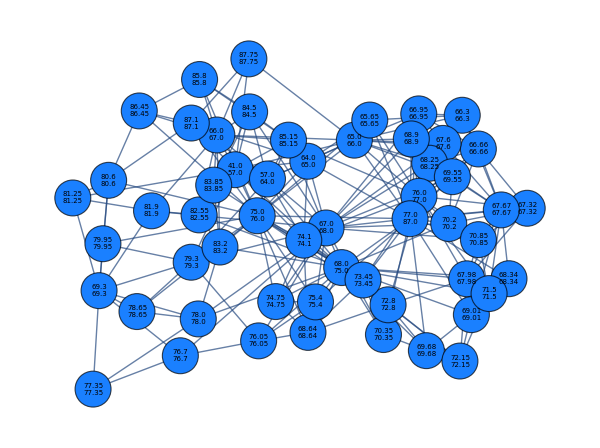
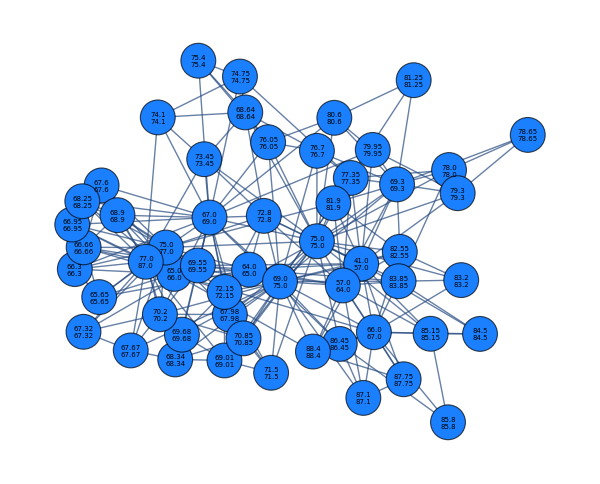
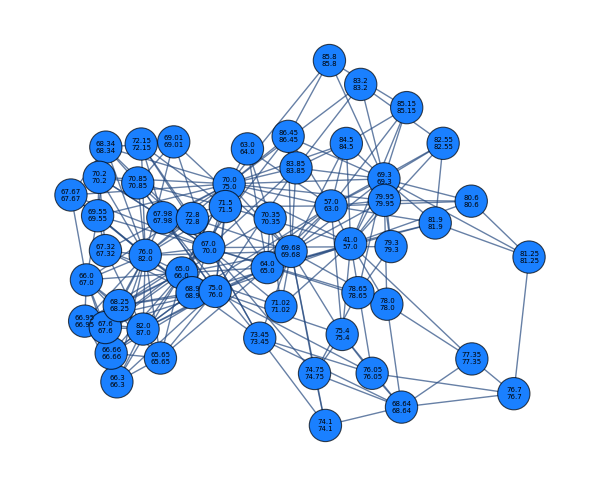
{{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55},{-Graphics-,55}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.767914,-0.845664},{0.829948,-0.829075},{0.629385,-0.868622},{0.729863,-0.79477},{0.727612,-0.853122},{0.678766,-0.873149},{0.778866,-0.877886},{0.678203,-0.862349},{0.863328,-0.853203},{0.726022,-0.85655}}

{{0.925784,-0.731837},{0.951473,-0.682085},{0.879689,-0.681712},{0.831552,-0.596759},{0.864873,-0.721212},{0.885541,-0.626575},{0.931057,-0.705016},{0.910229,-0.712981},{0.938219,-0.621927},{0.917204,-0.651067}}

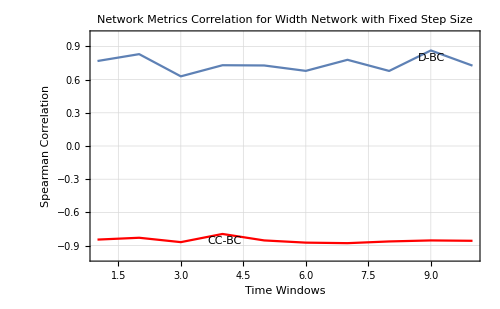
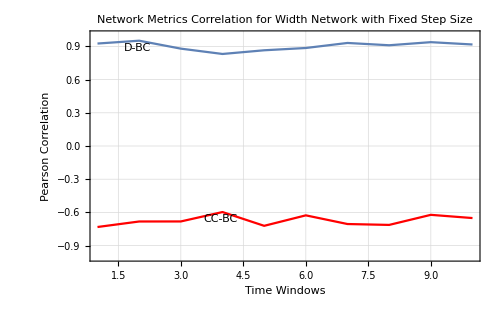

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-7.61033},{2,-4.95744},{3,-14.6055},{4,-8.65119},{5,-8.74502},{6,-10.2952},{7,-6.73297},{8,-10.547},{9,-3.03971},{10,-9.2238}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.65096},{2,-4.52137},{3,-4.92712},{4,-4.61019},{5,-5.03007},{6,-4.87373},{7,-4.99681},{8,-5.07192},{9,-4.9179},{10,-4.90242}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.0593356},{2,1.15447},{3,-2.19479},{4,-3.58037},{5,-2.2706},{6,-1.51536},{7,0.267788},{8,-0.603555},{9,0.515586},{10,-0.296038}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.21661},{2,-3.70766},{3,-3.88207},{4,-3.5312},{5,-4.53877},{6,-3.59823},{7,-4.27859},{8,-4.46446},{9,-3.61586},{10,-3.82381}}

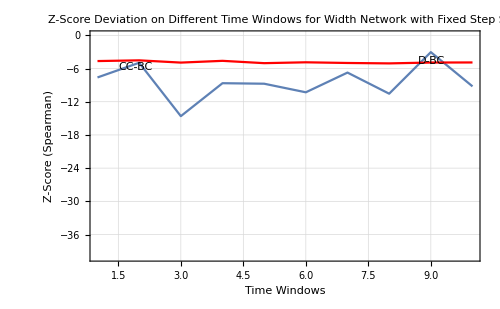
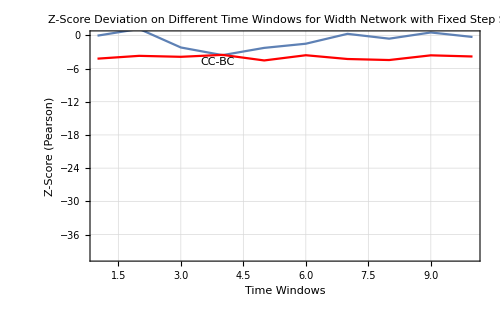

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```